```mathematica
Remove["Global`*"]
```

```mathematica
Get["/home/strelda/Documents/programování/Mathematica/packages/GRQUICK.m"]
"The convention for this program follow Sean M. Carroll's (Spacetime and Geometry) and the indices run from 0 \nto D-1.\n\nWhile working do not use the variables GARRAY,RARRAY,RsARRAY, CHARRAY, SPEEDOFLIGHT.  \n\nType ?helpGRQUICK for a list of functions or ?Function for a function description.\n\nMore functions and improvements coming soon!!"
```

Remove::rmnsm: There are no symbols matching "Global`*".

The convention for this program follow Sean M. Carroll's (Spacetime and Geometry) and the indices run from 0 
to D-1.

While working do not use the variables GARRAY,RARRAY,RsARRAY, CHARRAY, SPEEDOFLIGHT.  

Type ?helpGRQUICK for a list of functions or ?Function for a function description.

More functions and improvements coming soon!!'

The convention for this program follow Sean M. Carroll's (Spacetime and Geometry) and the indices run from 0 
to D-1.

While working do not use the variables GARRAY,RARRAY,RsARRAY, CHARRAY, SPEEDOFLIGHT.  

Type ?helpGRQUICK for a list of functions or ?Function for a function description.

More functions and improvements coming soon!!

```mathematica
<<"/home/strelda/Documents/programování/Mathematica/packages/GRQUICK/GRQUICKv4.m"
```

The convention for this program follow Sean M. Carroll's (Spacetime and Geometry) and the indices run from 0 
to D-1.

While working do not use the variables GARRAY,RARRAY,RsARRAY, CHARRAY, SPEEDOFLIGHT.  

Type ?helpGRQUICK for a list of functions or ?Function for a function description.

More functions and improvements coming soon!!'

### Analytic solution (just pretend we know energies)

```mathematica
energies=Eigenvalues[H[λ,0]];
g11=Re@Sum[(DH1[λ,χ][[1,i]])^2/(energies[[1]]-energies[[i]])^2,{i,2,2jj+1}]//FullSimplify;
g12=Re@Sum[(DH1[λ,χ][[1,i]]DH2[λ,χ][[1,i]])/(energies[[1]]-energies[[i]])^2,{i,2,2jj+1}]//FullSimplify;
g22=Re@Sum[(DH2[λ,χ][[1,i]])^2/(energies[[1]]-energies[[i]])^2,{i,2,2jj+1}]//FullSimplify;
gS={{g11,g12},{g12,g22}}
```

{{Re[∑_(i=2)^(1+2 jj) (DH1[λ,χ]⟦1,i⟧)^2/(H[λ,0]-Eigenvalues[H[λ,0]]⟦i⟧)^2],Re[∑_(i=2)^(1+2 jj) (DH1[λ,χ]⟦1,i⟧ DH2[λ,χ]⟦1,i⟧)/(H[λ,0]-Eigenvalues[H[λ,0]]⟦i⟧)^2]},{Re[∑_(i=2)^(1+2 jj) (DH1[λ,χ]⟦1,i⟧ DH2[λ,χ]⟦1,i⟧)/(H[λ,0]-Eigenvalues[H[λ,0]]⟦i⟧)^2],Re[∑_(i=2)^(1+2 jj) (DH2[λ,χ]⟦1,i⟧)^2/(H[λ,0]-Eigenvalues[H[λ,0]]⟦i⟧)^2]}}

## GRQUICK

```mathematica
gS={{(1+8 χ^2)/(16+λ (32+17 λ)),(8 λ χ)/(16+λ (32+17 λ))},{(8 λ χ)/(16+λ (32+17 λ)),(8 λ^2)/(16+λ (32+17 λ))}}
Metin[gS,{λ,χ}]
MatrixForm[GMET]
Einstein[0,0];
```

{{(1+8 χ^2)/(16+λ (32+17 λ)),(8 λ χ)/(16+λ (32+17 λ))},{(8 λ χ)/(16+λ (32+17 λ)),(8 λ^2)/(16+λ (32+17 λ))}}

Metric Success

((1+8 χ^2)/(16+λ (32+17 λ)) | (8 λ χ)/(16+λ (32+17 λ))
(8 λ χ)/(16+λ (32+17 λ)) | (8 λ^2)/(16+λ (32+17 λ)))

```mathematica
g1[λ_,χ_]:={{(1+8 χ^2)/(16+λ (32+17 λ)),(8 λ χ)/(16+λ (32+17 λ))},{(8 λ χ)/(16+λ (32+17 λ)),(8 λ^2)/(16+λ (32+17 λ))}}

dg[λ_,χ_]={ND[g1[l,χ],l,10,Terms->20]/.l->10,ND[g1[λ,c],c,2,Terms->40]/.c->2}
derg=dg[10,2]
ggg[μ_,α_,β_]:=1/2 Sum[Inverse[g1[10,2]][[μ,ν]](derg[[β,α,ν]]+derg[[α,ν,β]]-derg[[ν,β,α]]),{ν,1,2}]
ggg[1,1,1]
gg=1/2 Map[Inverse,g1](derg+Map[RotateLeft,derg]-RotateLeft[derg])
```

{{{-0.0000897403 (1.+8. χ^2),-0.00324995 χ},{-0.00324995 χ,0.00679324}},{{32./(16.+λ (32.+17. λ)),(8. λ)/(16.+λ (32.+17. λ))},{(8. λ)/(16.+λ (32.+17. λ)),0.}}}

{{{-0.00296143,-0.0064999},{-0.0064999,0.00679324}},{{0.0157171,0.0392927},{0.0392927,0.}}}

2.83202

{{{-0.0125892 g1,-0.0194997 g1},{-0.024377 g1,0.000146672 g1}},{{0.0289856 g1,0.0228963 g1},{0.0307549 g1,0.0162497 g1}}}

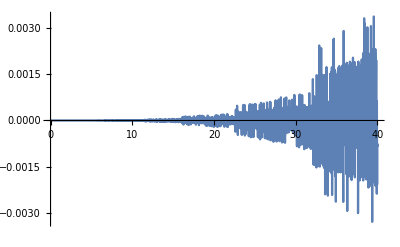

1/2 (2036 {{{-0.00296143,-0.0064999},{-0.0064999,0.00679324}},{{0.0157171,0.0392927},{0.0392927,0.}}}[10,2]⟦1,1,1⟧-2036/5 ({{{-0.00296143,-0.0064999},{-0.0064999,0.00679324}},{{0.0157171,0.0392927},{0.0392927,0.}}}[10,2]⟦1,1,2⟧+{{{-0.00296143,-0.0064999},{-0.0064999,0.00679324}},{{0.0157171,0.0392927},{0.0392927,0.}}}[10,2]⟦1,2,1⟧-{{{-0.00296143,-0.0064999},{-0.0064999,0.00679324}},{{0.0157171,0.0392927},{0.0392927,0.}}}[10,2]⟦2,1,1⟧))

```mathematica
g1[λ_,χ_]:={{(1+8 χ^2)/(16+λ (32+17 λ)),(8 λ χ)/(16+λ (32+17 λ))},{(8 λ χ)/(16+λ (32+17 λ)),(8 λ^2)/(16+λ (32+17 λ))}}
ggg[λ_?NumericQ,χ_?NumericQ]:=Module[{dg,derg,Γ},
dg={ND[g1[l,χ],l,λ,Terms->20],ND[g1[λ,c],c,χ,Terms->20]};
derg=dg;
ggg[μ_,α_,β_]:=1/2 Sum[Inverse[g1[λ,χ]][[μ,ν]](derg[[β,α,ν]]+derg[[α,ν,β]]-derg[[ν,β,α]]),{ν,1,2}];
ggg[2,1,1]
]
Plot[ggg[1,x]-Christoffel[{{1},{0,0}}]/.{λ->1,χ->x},{x,0,40},PlotRange->Full]
```

```mathematica
Setlight[1];
MatrixForm@Geodesics[τ]
```

```mathematica
init={3,0.5};
vin={1,1};
vinit=vin/(√(-vin.gS.vin))/.{λ->init[[1]],χ->init[[2]]}
MatrixForm[Geodesics[τ]]
Geoplot[τ,init,vinit,{0,10},{λ,χ}]
```

{0.-1.63608 ⅈ,0.-1.63608 ⅈ}

(((16+17 λ[τ]) (-1+8 χ[τ]^2) λ'[τ]^2)/(16+32 λ[τ]+17 λ[τ]^2)+(16 λ[τ] (16+17 λ[τ]) χ[τ] λ'[τ] χ'[τ])/(16+32 λ[τ]+17 λ[τ]^2)+(4 λ[τ]^2 (32+34 λ[τ]) χ'[τ]^2)/(16+λ[τ] (32+17 λ[τ]))+λ''[τ]
-((16+17 λ[τ]) χ[τ] (1+8 χ[τ]^2) λ'[τ]^2)/(λ[τ] (16+32 λ[τ]+17 λ[τ]^2))-(16 (-2+17 λ[τ]^2 χ[τ]^2+2 λ[τ] (-1+8 χ[τ]^2)) λ'[τ] χ'[τ])/(λ[τ] (16+32 λ[τ]+17 λ[τ]^2))-(4 λ[τ] (32+34 λ[τ]) χ[τ] χ'[τ]^2)/(16+λ[τ] (32+17 λ[τ]))+χ''[τ])

{-Graphics-,-Graphics-}

### Metric tensor analytically using stationary perturbation method to find energies

```mathematica
H0d[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]+λ/(2j)V1[jp,mp,j,m];
Hpd[jp_,mp_,j_,m_]:=λ/(2j)(χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m]);
jj=1;  (*jj=N/2*)
f[mp_,m_]:=H0d[jj,mp,jj,m]
H0[λ_,χ_]=Table[f[r,z],{r,-jj,jj},{z,-jj,jj}];
fp[mp_,m_]:=Hpd[jj,mp,jj,m]
Hp[λ_,χ_]=Table[fp[r,z],{r,-jj,jj},{z,-jj,jj}];
```

```mathematica
N@Eigenvalues[H0[-3,1]]
N@Eigenvalues[Hp[-3,1]]
```

{-10.0697,-6.,-1.93029}

{-10.6439,3.80974,-0.665837}

```mathematica
H0[χ]//MatrixForm
Hp[λ,χ]//MatrixForm
```

(-1 | 0 | 0
0 | 0 | 0
0 | 0 | 1)

(3 | χ/(√2) | 1/4
χ/(√2) | 1/2 (4+χ^2) | (3 χ)/(√2)
1/4 | (3 χ)/(√2) | 1/2 (2+4 χ^2))

```mathematica
e0=Eigenvalues[H0[χ]]
psi0=Eigenvectors[H0[χ]]
```

{-1,1,0}

{{1,0,0},{0,0,1},{0,1,0}}

```mathematica
e1=Conjugate@psi0[[#]].(Hp[λ,χ]. psi0[[#]])&/@Range[1,2jj+1]
e2=Sum[(Conjugate@psi0[[#]].(Hp[λ,χ]. psi0[[#]]))^2/(e0[[#]]-e0[[j]]),{j,DeleteCases[Range[1,2jj+1],#]}]&/@Range[1,2jj+1]
```

{3,1/2 (2+4 χ^2),1/2 (4+χ^2)}

{-27/2,3/8 (2+4 χ^2)^2,0}

```mathematica
en[λ_]:=e0+λ e1+λ^2 e2/.χ->1
```

```mathematica
Det[H[λ,χ]-a IdentityMatrix[2jj+1]]
```

a-a^3+2 λ+2 a λ-6 a^2 λ+4 λ^2-(175 a λ^2)/16-(47 λ^3)/8+(λ χ^2)/2-2 a λ χ^2-5/2 a^2 λ χ^2+λ^2 χ^2-7 a λ^2 χ^2-(7 λ^3 χ^2)/32-λ^2 χ^4-a λ^2 χ^4-2 λ^3 χ^4

```mathematica
1.1^2(1-2/r)
```

1.21 (1-2/r)

```mathematica
-vin.GMET.vin
```

-2/(-2-100 (1-2/r))-(100 (1-2/r))/(-2-100 (1-2/r))

```mathematica
vin.GMET.vin
```

2+4 (1-2/r)

# Testing GRQUICK

```mathematica
Metin[DiagonalMatrix[{2,(1-2/r)}],{t,r}]
MatrixForm[Geodesics[τ]]
Setlight[1];
init={0,1.1};
vin={"Max",20};
(*vinit=vin/(√(-(2+4 (1-2/r))))/.{t->init[[1]],r->init[[2]]}*)
Geoplot[τ,init,vin,{0,3},{t,r}]
```

Metric Success

(t''[τ]
r'[τ]^2/((-2+r[τ]) r[τ])+r''[τ])

NDSolve::ndsz: At τ == 0.0262921, step size is effectively zero; singularity or stiff system suspected.

{-Graphics-,-Graphics-}

```mathematica
vinit=vin/(√(vin.GMET.vin))
```

```mathematica
{1/(√(-1+2/r)),0,0,0}/.r->3
```

{-ⅈ √3,0,0,0}

```mathematica
GMET.vin
```

{-1+2/r,0,0,0}

```mathematica
ResourceFunction["Geodesic"]
```

```mathematica
ge=ResourceFunction["Geodesic"][gS[u,v],{u,v},t,{0.1,0.1},θ]
sg=Flatten[(NDSolve[#1,{u,v},{t,0,4}]&)/@Table[ge,{θ,(2 π)/30,2 π,(2 π)/30}],1];
hS[u[t],v[t]]/.sg[[1]]/.t->.1
ParametricPlot[Evaluate[{u[t],v[t]}/.sg],{t,0,π},PlotRange->All,PlotStyle->Hue[0]]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{{u''[t],Indeterminate},{Indeterminate,u''[t]}}==0,{{v''[t],Indeterminate},{Indeterminate,v''[t]}}==0,u[0]==0.1,v[0]==0.1,u'[0]==Cos[θ],v'[0]==Sin[θ]}

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::nlnum: The function value {0.,{{0.,Indeterminate},{Indeterminate,0.}},0.,{{0.,Indeterminate},{Indeterminate,0.}}} is not a list of numbers with dimensions {4} at {t,u[t],u'[t],v[t],v'[t],u'[t],u''[t],v'[t],v''[t]} = {0.,0.1,0.978148,0.1,0.207912,0.978148,0.,0.207912,0.}.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::nlnum: The function value {0.,{{0.,Indeterminate},{Indeterminate,0.}},0.,{{0.,Indeterminate},{Indeterminate,0.}}} is not a list of numbers with dimensions {4} at {t,u[t],u'[t],v[t],v'[t],u'[t],u''[t],v'[t],v''[t]} = {0.,0.1,0.913545,0.1,0.406737,0.913545,0.,0.406737,0.}.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

General::stop: Further output of NDSolve::ntdvdae will be suppressed during this calculation.

NDSolve::nlnum: The function value {0.,{{0.,Indeterminate},{Indeterminate,0.}},0.,{{0.,Indeterminate},{Indeterminate,0.}}} is not a list of numbers with dimensions {4} at {t,u[t],u'[t],v[t],v'[t],u'[t],u''[t],v'[t],v''[t]} = {0.,0.1,0.809017,0.1,0.587785,0.809017,0.,0.587785,0.}.

General::stop: Further output of NDSolve::nlnum will be suppressed during this calculation.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

General::stop: Further output of NDSolve::icfail will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

hS[u[0.1],v[0.1]]/.{}⟦1⟧

-Graphics-

```mathematica
,
```